```mathematica
1+2
```

3

```mathematica
4
```

4

```mathematica
range[4]
```

range[4]

```mathematica
range[10]
```

range[10]

```mathematica
% + %
```

2 range[10]

```mathematica
x-x
```

0

```mathematica
Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
e
```

e

```mathematica
e -1
```

-1+e

```mathematica
x-1
```

-1+x

```mathematica
{1,2,3,4,5, 6}
```

{1,2,3,4,5,6}

```mathematica
{1,2,3,4,5, 6}[[4]]
```

4

```mathematica
Table[x^2,{x,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Sunset[]
```

Minute: Sun 20 Aug 2017 18:53GMT+8.

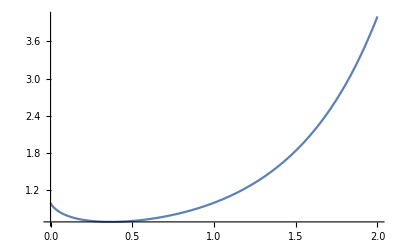

```mathematica
Plot[x^x,{x,0,2}]
```

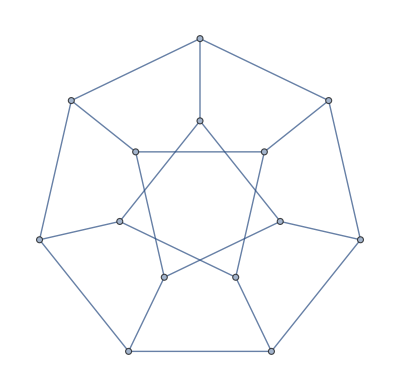

```mathematica
PetersenGraph[7,2]
```

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

```mathematica
Rotate[Rectangle,Pi/2]
```

Rectangle

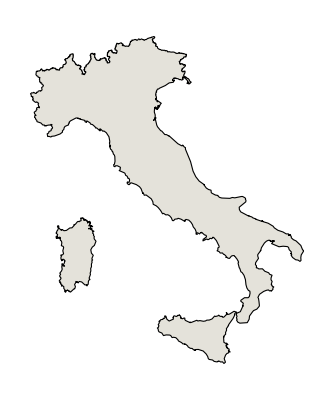

```mathematica
CountryData["ITA","Shape"]
```

```mathematica
CountryData["China","economy"]
```

$Failed

```mathematica
(#1->CountryData["China",#1]&)/@{"GDP","GDPAtParity","GDPPerCapita","GDPRealGrowth","GDPSectorFractions"}
```

{GDP→1.03548×10^13 $,GDPAtParity→1.80171×10^13 $,GDPPerCapita→7590.02 $,GDPRealGrowth→0.0726846 $,GDPSectorFractions→{AgriculturalValueAdded→0.116132 $,ConstructionValueAdded→0.055798 $,IndustrialValueAdded→0.427557 $,MiscellaneousValueAdded→0.258816 $,TradeValueAdded→0.0828428 $,TransportationValueAdded→0.0588541 $}}

```mathematica
Graphics3D@{Sphere[],Cone[]}
```

-Graphics3D-

```mathematica
Piecewise[{{13+2x^2,x>0}},13]
```

Piecewise[{{13+2 x^2, x>0}, {13, True}}]

```mathematica
Solve[a*x^4+b*x^3+c*x^2+d*x==0,x]
```

{{x→0},{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+1/(3 2^(1/3) a)(-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-1/(6 2^(1/3) a)(1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-1/(6 2^(1/3) a)(1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3)}}

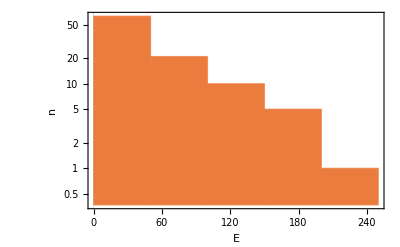

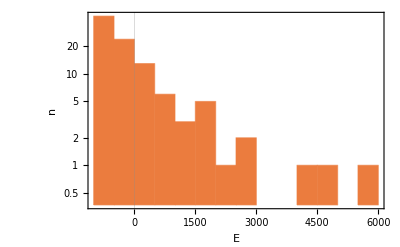

```mathematica
change[n_,m_,t_]:=Module[{M=Table[m,{n}],a,b,s},Do[a=RandomInteger[{1,n}];
b=RandomInteger[{1,n}];
s=RandomInteger[{1,n m}];
If[M[[a]]≥s,M[[a]]=M[[a]]-s;M[[b]]=M[[b]]+s];,{t}];
M]
Histogram[change[100,50,100000],ScalingFunctions->"Log",PlotTheme->"Scientific",FrameLabel->{"E",n}]

change2[n_,m_,t_,limit_]:=Module[{M=Table[m,{n}],a,b,s},Do[a=RandomInteger[{1,n}];
b=RandomInteger[{1,n}];
s=RandomInteger[{1,n m}];
If[M[[a]]+limit≥s,M[[a]]=M[[a]]-s;M[[b]]=M[[b]]+s];,{t}];
M]
Histogram[change2[100,50,200000,1000],ScalingFunctions->"Log",PlotTheme->"Scientific",FrameLabel->{"E",n}]
```

```mathematica
IntegerExponent[FromDigits/@Permutations[Range[9]],3]//Max
```

13

```mathematica
$Version
```

11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017)